```mathematica
alexa={0.09236105267670168,0.02436420495950694,0.03710253135215547,0.03254229901517954,0.09985992941299747,0.016848955563211566,0.024686200606165488,0.025608527119475567,0.07407418065255668,0.005654620622645314,0.01868884563419548,0.04738098961516906,0.03363351199709142,0.0613452809429382,0.07328124776736454,0.028014712769960357,0.0020687103980084496,0.06434822524334734,0.06625985733360218,0.06191961401007524,0.03324771259055569,0.013106562400275617,0.012937179790461705,0.006632812636438833,0.01807829425857451,0.007033694735822666,0.0024132308556967332,0.003217574988767363,0.002961069982107163,0.0019240356205575517,0.0018467368197110155,0.0013791733414197736,0.0012297356083326321,0.0011519406662739875,0.0015328778889310498,0.001263870123725711};
```

```mathematica
SetDirectory["E:\\Working\\captures\\query-processing"]
```

E:\Working\captures\query-processing

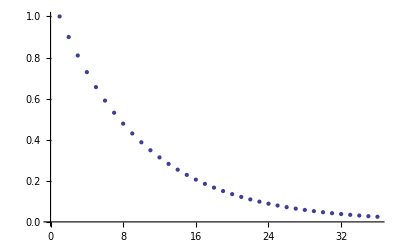

```mathematica
expscale=Table[0.9^i,{i,0,35}];
ListPlot[expscale]
```

```mathematica
tunpdfs=Import["tun.born.pdfs.csv"];
```

```mathematica
qrpdfs=Import["qr.born.pdfs.csv"];
```

```mathematica
qravg=Mean[qrpdfs];
tunavg=Mean[tunpdfs];
```

```mathematica
qrsavg=Mean[Map[Reverse[Sort[#]]&,qrpdfs]];
tunsavg=Mean[Map[Reverse[Sort[#]]&,tunpdfs]];
```

```mathematica
Show[
ListPlot[Map[Mean[Map[Reverse[Sort[#]]&,#]]&,Partition[qrpdfs,Floor[Length[qrpdfs]/5000]]],Joined->True,PlotRange->All,PlotStyle->Red],
ListPlot[Map[Reverse[Sort[Map[Mean,Transpose[#]]]]&,Partition[tunpdfs,Floor[Length[tunpdfs]/100]]],Joined->True,PlotRange->All,PlotStyle->Blue],
ListPlot[{qrsavg,tunsavg,Reverse[Sort[alexa]],qravg,tunavg,alexa},PlotStyle->{{Thick,Purple},{Thick,Green},{Thick,Black}},Joined->True]
]
```

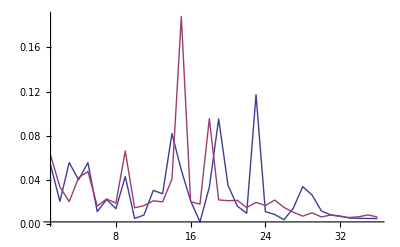

```mathematica
ListPlot[{qravg,tunavg},Joined->True,PlotRange->All]
```

```mathematica
tuntunli=ListInterpolation[Map[Norm[#-tunavg]&,tunpdfs]//Sort,{{0,1}}];
tunstunli=ListInterpolation[Map[Norm[Reverse[Sort[#]]-tunsavg]&,tunpdfs]//Sort,{{0,1}}];
tunqrli=ListInterpolation[Map[Norm[#-qravg]&,tunpdfs]//Sort,{{0,1}}];
tunsqrli=ListInterpolation[Map[Norm[Reverse[Sort[#]]-qrsavg]&,tunpdfs]//Sort,{{0,1}}];
tunali=ListInterpolation[Map[Norm[#-alexa]&,tunpdfs]//Sort,{{0,1}}];
tunsali=ListInterpolation[Map[Norm[Reverse[Sort[#]]-Reverse[Sort[alexa]]]&,tunpdfs]//Sort,{{0,1}}];
```

```mathematica
tunseqrli=ListInterpolation[Map[Norm[expscale(Reverse[Sort[#]]-qrsavg)]&,tunpdfs]//Sort,{{0,1}}];
qrseqrli=ListInterpolation[Map[Norm[expscale(Reverse[Sort[#]]-qrsavg)]&,qrpdfs]//Sort,{{0,1}}];
```

```mathematica
tunseali=ListInterpolation[Map[Norm[expscale(Reverse[Sort[#]]-Reverse[Sort[alexa]])]&,tunpdfs]//Sort,{{0,1}}];
qrseali=ListInterpolation[Map[Norm[expscale(Reverse[Sort[#]]-Reverse[Sort[alexa]])]&,qrpdfs]//Sort,{{0,1}}];
```

```mathematica
Norm[Reverse[Sort[alexa]]-Reverse[Sort[qrsavg]]]
```

0.230754

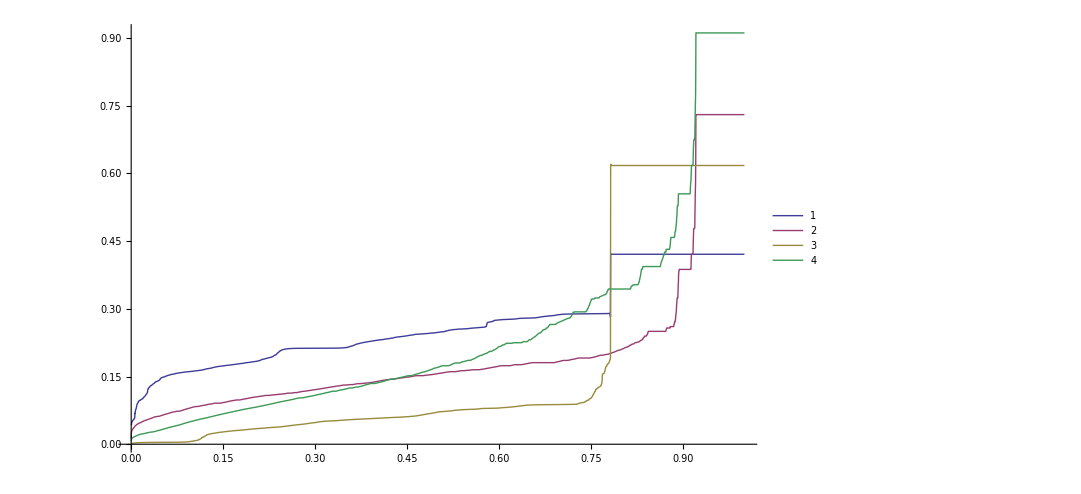

```mathematica
Plot[{tunseqrli[t],qrseqrli[t],tunseali[t],qrseali[t]},{t,0,1},PlotRange->All,ImageSize->800,PlotLegends->Automatic]
```

```mathematica
qrtunli=ListInterpolation[Map[Norm[#-tunavg]&,qrpdfs]//Sort,{{0,1}}];
qrstunli=ListInterpolation[Map[Norm[Reverse[Sort[#]]-tunsavg]&,qrpdfs]//Sort,{{0,1}}];
qrqrli=ListInterpolation[Map[Norm[#-qravg]&,qrpdfs]//Sort,{{0,1}}];
qrsqrli=ListInterpolation[Map[Norm[Reverse[Sort[#]]-qrsavg]&,qrpdfs]//Sort,{{0,1}}];
qrali=ListInterpolation[Map[Norm[#-alexa]&,qrpdfs]//Sort,{{0,1}}];
qrsali=ListInterpolation[Map[Norm[Reverse[Sort[#]]-Reverse[Sort[alexa]]]&,qrpdfs]//Sort,{{0,1}}];
```

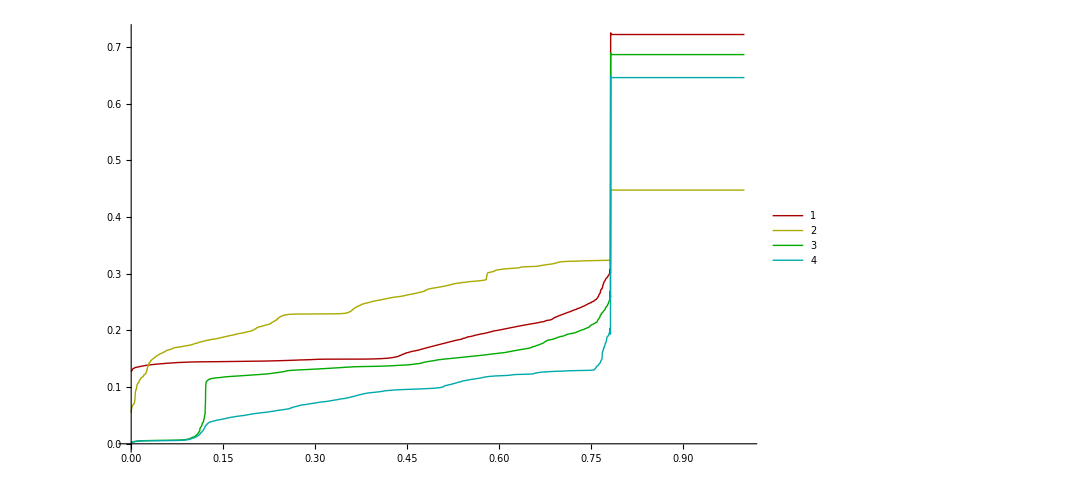

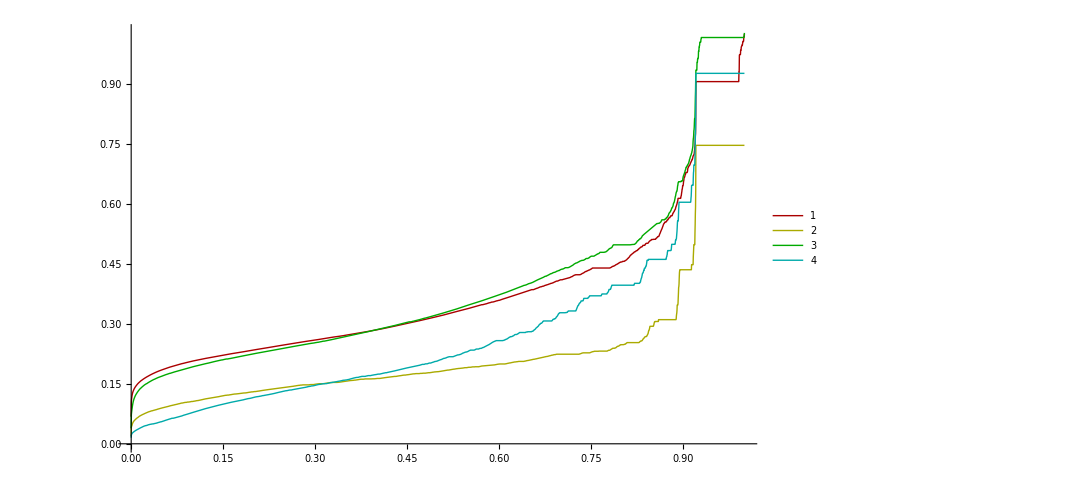

```mathematica
Plot[{tunqrli[t],tunsqrli[t],tunali[t],tunsali[t]},{t,0,1},PlotStyle->Table[Darker[Hue[i/6]],{i,0,5}],PlotLegends->Automatic,ImageSize->800]
Plot[{qrqrli[t],qrsqrli[t],qrali[t],qrsali[t]},{t,0,1},PlotStyle->Table[Darker[Hue[i/6]],{i,0,5}],PlotLegends->Automatic,ImageSize->800]
```

```mathematica
tunmseli=ListInterpolation[Map[Norm[#-Mean[#]]&,tunpdfs]//Sort,{{0,1}}];
qrmseli=ListInterpolation[Map[Norm[#-Mean[#]]&,qrpdfs]//Sort,{{0,1}}];
```

Power::infy: Infinite expression 1/0. encountered.

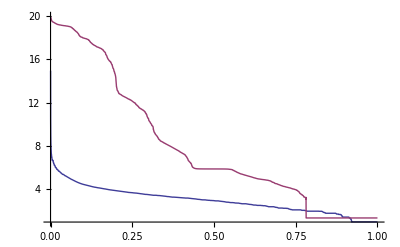

```mathematica
Plot[{1/qrmseli[t],1/tunmseli[t]},{t,0,1},PlotRange->All]
```

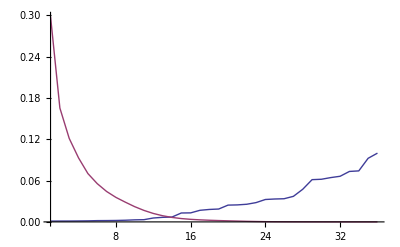

{0.388502,0.102484,0.156066,0.136884,0.420045,0.0708725,0.103839,0.107718,0.311581,0.0237853,0.0786117,0.199301,0.141474,0.258039,0.308246,0.11784,0.00870171,0.270671,0.278712,0.260455,0.139851,0.0551307,0.0544182,0.0278999,0.0760435,0.0295861,0.0101509,0.0135342,0.0124553,0.00809316,0.00776801,0.00580128,0.00517269,0.00484546,0.00644781,0.00531627}

0.713105

```mathematica
target={0.09236105267670168,0.02436420495950694,0.03710253135215547,0.03254229901517954,0.09985992941299747,0.016848955563211566,0.024686200606165488,0.025608527119475567,0.07407418065255668,0.005654620622645314,0.01868884563419548,0.04738098961516906,0.03363351199709142,0.0613452809429382,0.07328124776736454,0.028014712769960357,0.0020687103980084496,0.06434822524334734,0.06625985733360218,0.06191961401007524,0.03324771259055569,0.013106562400275617,0.012937179790461705,0.006632812636438833,0.01807829425857451,0.007033694735822666,0.0024132308556967332,0.003217574988767363,0.002961069982107163,0.0019240356205575517,0.0018467368197110155,0.0013791733414197736,0.0012297356083326321,0.0011519406662739875,0.0015328778889310498,0.001263870123725711};
ListPlot[{Sort[target],qrsavg},Joined->True,PlotRange->All]
target=target/Norm[target]
Norm[target-Mean[target]]
```

```mathematica
Norm[tunavg-Mean[tunavg]]
Norm[tunsavg-Mean[tunsavg]]
Norm[qravg-Mean[qravg]]
Norm[qrsavg-Mean[qrsavg]]
```

0.197983

0.240254

0.16027

```mathematica
Ordering[Table[RandomReal,{Length[qrsavg]}]]
```

{33,24,7,34,8,3,28,23,17,29,19,21,31,10,15,30,27,6,13,22,12,2,32,14,4,9,35,25,26,18,5,36,11,1,16,20}

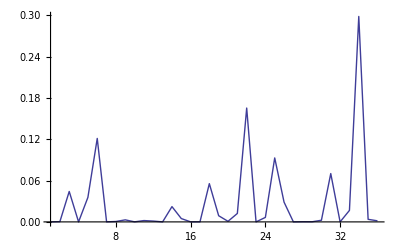

```mathematica
o=Ordering[Table[RandomReal[],{Length[qrsavg]}]]
ListPlot[qrsavg[[o]],Joined->True,PlotRange->All]
Transpose[
{Join[
Map[FromCharacterCode,ToCharacterCode["0"][[1]]-1+Select[o,#≤10&]],
Map[FromCharacterCode,ToCharacterCode["a"][[1]]-1+Select[o-10,#>0&]]
],qrsavg}
]
```

```mathematica
Transpose[
{Join[
Map[FromCharacterCode,ToCharacterCode["0"][[1]]-1+Select[o,#≤10&]],
Map[FromCharacterCode,ToCharacterCode["a"][[1]]-1+Select[o-10,#>0&]]
],Floor[1000000qrsavg]}
]
```

{{6,298340},{7,165347},{2,121219},{9,92895},{5,70191},{1,55552},{3,44196},{8,35590},{4,28695},{0,22173},{w,16683},{n,12268},{x,8942},{r,6509},{m,4843},{g,3721},{s,2961},{i,2393},{k,1934},{u,1552},{e,1195},{t,836},{q,582},{c,363},{l,249},{b,180},{v,134},{d,99},{y,74},{o,54},{p,39},{h,26},{z,16},{a,10},{f,5},{j,2}}